```mathematica
ToDipict=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\ESSResultAZ.csv","CSV"]];
```

```mathematica
Length[ToDipict]
```

110773

```mathematica
allnpc=0;
For[i=1,i≤Length[ToDipict],i++,
If[Round[ToDipict[[i,1]]]==1,allnpc=allnpc+1,]
];
allnpc
```

51

```mathematica
countTwoTypes[lst_,len_]:=Block[{npc,smc},
npc=0;
smc=0;
For[i=1,i≤Length[lst],i++,
If [lst[[i,2]]<len,If[Round[lst[[i,1]]]==0,smc=smc+1,npc=npc+1],]
];
Return[{npc,smc}]
];
```

```mathematica
Table[countTwoTypes[ToDipict,6.0+(n-1)*0.1],{n,1,201}]
```

{{0,1},{0,1},{0,1},{0,1},{1,1},{2,2},{2,2},{2,2},{2,2},{2,2},{2,3},{3,3},{4,3},{5,3},{5,3},{5,3},{5,3},{5,3},{5,4},{6,4},{6,5},{6,5},{6,5},{6,5},{6,5},{6,5},{6,5},{6,5},{7,5},{7,6},{8,6},{8,7},{9,7},{9,8},{10,8},{10,9},{10,10},{10,10},{10,10},{10,10},{11,10},{11,10},{11,10},{11,10},{12,10},{12,11},{12,11},{12,11},{12,12},{13,12},{13,12},{13,12},{13,13},{13,13},{13,13},{13,14},{13,14},{15,15},{15,15},{15,15},{15,15},{15,16},{15,16},{15,17},{15,18},{15,18},{15,21},{16,21},{17,23},{17,23},{17,23},{18,23},{19,24},{19,26},{19,26},{19,28},{19,30},{19,32},{19,33},{19,36},{19,39},{20,39},{21,40},{21,41},{21,42},{21,43},{21,44},{21,45},{23,47},{23,50},{23,52},{23,53},{23,56},{24,59},{24,59},{24,61},{24,65},{24,68},{24,71},{24,73},{24,74},{25,78},{25,79},{25,81},{26,83},{26,85},{26,87},{26,90},{27,93},{27,95},{28,96},{29,100},{29,102},{29,103},{29,105},{29,109},{29,116},{29,120},{29,124},{29,129},{29,130},{29,133},{29,134},{30,139},{30,139},{30,147},{30,154},{30,156},{30,158},{31,161},{32,167},{32,173},{33,178},{33,181},{35,187},{35,189},{35,194},{35,196},{35,202},{36,208},{37,213},{37,217},{37,219},{37,225},{37,235},{38,240},{38,244},{39,247},{39,251},{39,258},{39,260},{40,266},{40,269},{40,273},{40,279},{40,285},{41,290},{41,298},{42,302},{42,306},{42,314},{42,320},{42,329},{42,337},{42,342},{42,347},{43,353},{43,363},{43,371},{44,378},{44,390},{44,401},{45,407},{45,414},{46,422},{46,429},{46,439},{46,446},{46,454},{46,463},{46,475},{46,479},{46,489},{46,498},{46,513},{46,520},{46,526},{46,536},{46,547},{46,556},{46,565},{47,575},{47,579},{47,590},{47,602},{47,612},{48,621},{48,627},{49,636},{50,644},{50,657}}

```mathematica
listSM={};
listA0={};
listA1={};
listA2={};
listA3={};
listA4={};
For[i=1,i<=Length[ToDipict],i++,
If[Round[ToDipict[[i,1]]]==0,AppendTo[listSM,ToDipict[[i,2]]]];
If[Round[ToDipict[[i,1]]]==1,AppendTo[listA0,ToDipict[[i,2]]]];
If[Round[ToDipict[[i,1]]]==2,AppendTo[listA1,ToDipict[[i,2]]]];
If[Round[ToDipict[[i,1]]]==3,AppendTo[listA2,ToDipict[[i,2]]]];
If[Round[ToDipict[[i,1]]]==4,AppendTo[listA3,ToDipict[[i,2]]]];
If[Round[ToDipict[[i,1]]]==5,AppendTo[listA4,ToDipict[[i,2]]]];
]
```

```mathematica
listA1
```

{8.02,10.78,16.16,10.24,5.44,16.96,13.88,10.48,14.14,16.4,8.54,6.26,22.52,19.44,16.22,7.42,18.2,14.68,19.74,7.08}

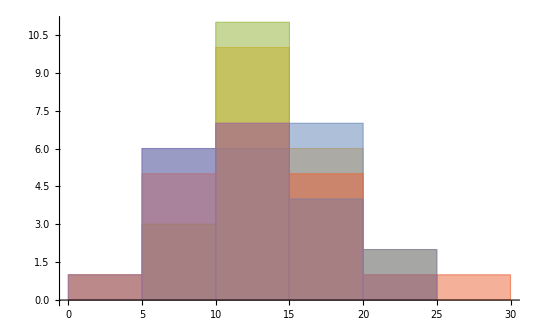

```mathematica
Histogram[{listA0,listA1,listA2,listA3,listA4},5]
```

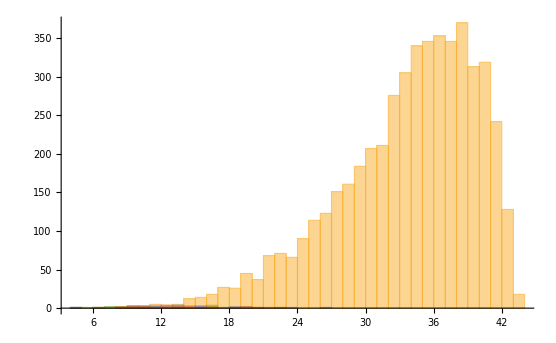

```mathematica
Histogram[{listSM,listA0,listA1,listA2,listA3,listA4},50]
```